### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
𝒞[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1)}]
𝒫[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2}]
ℛ[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω1/ω2,ω2->1/ω2}]
𝒮[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1}]
```

```mathematica
EXPR[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=Through[Through[(ℳ0+𝒫[ℳ0[ω1,ω2]]+𝒞[ℳ0[ω1,ω2]]+ℛ[ℳ0[ω1,ω2]]+𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]][ω1,ω2]]+ℳ1[Ma,Mb,Mc,Md]+ℛ[ℳ1[Ma,Mb,Mc,Md][ω1,ω2]])[ω1,ω2]][ϕ1,ϕ2,ϕ3,ϕ4]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],0]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
ℳ1[Ma_,Mb_,Mc_,Md_][ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=((#+𝒮[#][ω1,ω2])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0]])+((#+𝒞[#][ω1,ω2])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
If[ω2>ω1,-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]),0]])+((#+𝒮[#][ω1,ω2]+𝒫[#][ω1,ω2]+𝒞[#][ω1,ω2])&[If[(ω2>ω1)&&(ω1>1),-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}],0]])
```

```mathematica
ℳone[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR[ω1,ω2][Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 1.*)
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 2*)
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1);(*transform ω1 to ω2, your definition, solution 2*)
```

```mathematica
Sz[z_][M1_,M2_]:=M1^2/(1-z)+M2^2/z;(*Centre of mass energy*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
zfω1[ω1_][MA_,MB_,MC_,MD_]:=ω1/(1+ω2n[ω1][MA,MB,MC,MD])(*transform ω1 to z, using z=ω1/(1+ω2) and previous result of ω1 to ω2*)
ωfω1[ω1_][MA_,MB_,MC_,MD_]:=(ω2n[ω1][MA,MB,MC,MD])/(1+ω2n[ω1][MA,MB,MC,MD]);
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
ω2fz[z_][M1_,M2_,M3_,M4_]:=(-ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1);(*transform z to ω1 and ω2, using z=ω1/(1+ω2) and previous result of z to ω*)
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine,Mseq},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"Yes"->True,"No"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Mseq=Sequence[M1,M2,M3,M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
Print["ω1=",ω1,"    ω2=",ω2];(*it's for debug purpose, you can comment this*){Sen,ℳone[ω1,ω2][M1,M2,M3,M4][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]],{ω1,0.003,Which[n1==0&&n2==0,0.99,n1<2&&n2<2,ω1/.Last@FindMinimum[Sω1[ω1][Mseq],{ω1,0.99}],True,ω1/.Last@FindMinimum[Sω1[ω1][Mseq],{ω1,0.9}]],0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

Function structure is Msum[<one flavour quark mass>][(excited state)<1>,<2>,<3>,<4>]

```mathematica
Msumdat=Msum[60][2,2,0,0]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=120.335  M4=120.335

ω1=0.003    ω2=0.00296194

ω1=0.083    ω2=0.0818564

ω1=0.163    ω2=0.160543

ω1=0.243    ω2=0.238956

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0226737,0.0000680699}. NIntegrate obtained 8.6495173540018562825344256036184713332620342585991124749426887737×10^1636-5.4818926736158931760620058077218744853870831255559562638704283899×10^1623 ⅈ and 2.3692992000779514745785687076405086626050506042823518694461565467×10^1637 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0299326,3.22008×10^-6}. NIntegrate obtained -2.9874428616186394339571469358916586550198864783799890322215406518×10^3096+9.3979894005873025981309806372593771462201632132173923360622964187×10^3083 ⅈ and 7.0566614615432110275231725383269863340425029787533422749978874651×10^3096 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0226737,0.000144364}. NIntegrate obtained 8.4084464994201844580459627547288420809652024043958385850850997287×10^1325-5.7331716312129743098769721976526032756724519463820016668477449799×10^1312 ⅈ and 1.3129636149626618110467071554829339290279025057175047547733176773×10^1326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

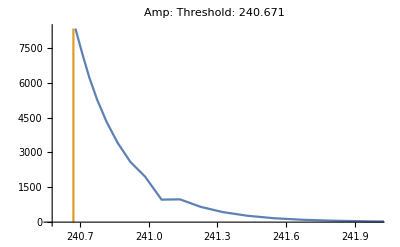

```mathematica
ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

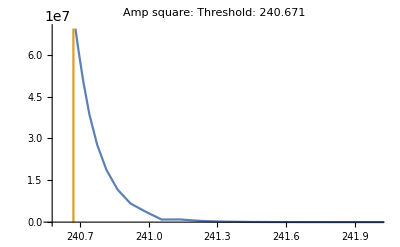

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Clear[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4,ΦB,ϕxB]
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
Mseq=Sequence[M1,M2,M3,M4];
```

Wavefunction build complete.

```mathematica
?ℳ1
```

```mathematica
Block[{ω1=0.163,ω2},ω2=ω2p[ω1][Mseq]]
```

0.160543

```mathematica
Block[{ω1=0.163,ω2},ω2=ω2p[ω1][Mseq];
EXPR[ω1,ω2][Mseq][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.000508235

```mathematica
Block[{ω1=0.163,ω2},ω2=ω2p[ω1][Mseq];
ℳone[ω1,ω2][Mseq][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.000508235

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2p[ω1][Mseq];ℳ1[Mseq][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

-1.17951×10^-7

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2p[ω1][Mseq];ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0

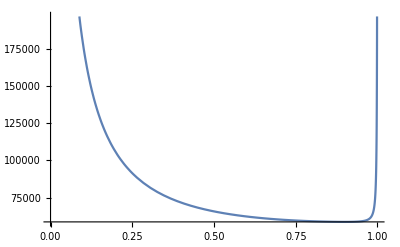

```mathematica
Plot[Sω1[ω1][Mseq],{ω1,0,1}]
```

```mathematica
ω1/.Last@FindMinimum[Sω1[ω1][Mseq],{ω1,0.9}]
```

0.898903